```mathematica
MullerDat =Transpose[Import["Location/MullerMatrix.dat", "Table"]];
GenotypeDat =Import["Location/Genotype_Frequencies.dat", "Table"];
SimilarityDat = Import["Location/SignificantParallelMutations.dat", "List"];
Clumpiness = Import["Location/SweepClumpiness.dat", "List"];
TimeDat = Import["Location/TimeToSweep.dat", "List"];
```

```mathematica
MullerPlot =ArrayPlot[MullerDat, 
					ColorFunction->(Darker[Hue[33Pi#]]&),
					AspectRatio->1/4,
					ImageSize->1000,
					(*ColorFunction->"Monochrome",*)
					(*ColorFunction->(RGBColor[2*#,#,0]&),*)
					Frame->None];
Show[MullerPlot, 
Frame->True,
PlotLabel->Style["Genotype Frequencies Muller Representation",50],
FrameLabel ->Style["Generations (In Thousands)",40],
FrameStyle->{{Transparent,Transparent},{{Thick,35},Transparent}},
FrameTicks->{{None,None},{{{0,0},{4000/6.64, 4},
{8000/6.64, 8}, {12000/6.64, 12}, 
{16000/6.64, 16},  {20000/6.64, 20},
{24000/6.64, 24},  {28000/6.64, 28},
{32000/6.64, 32},  {36000/6.64, 36},
{40000,6.63, 40}},None}},
Axes->{False,False}]
```

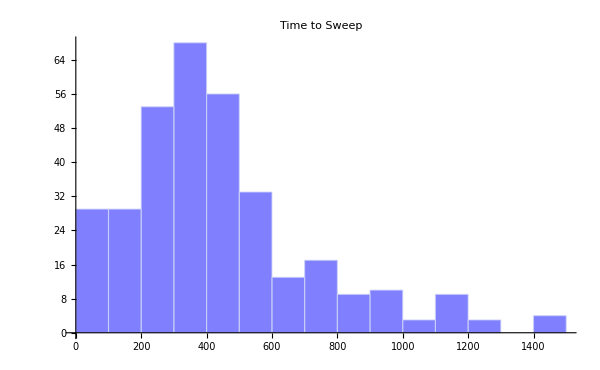

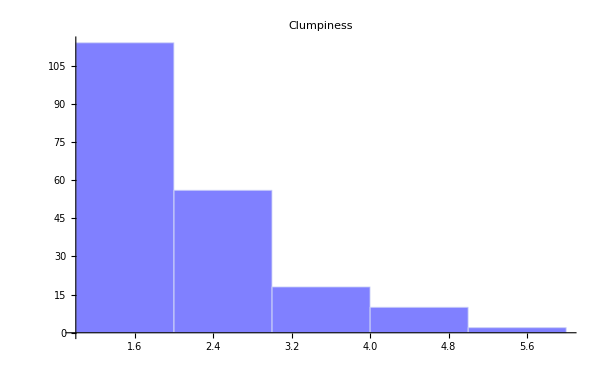

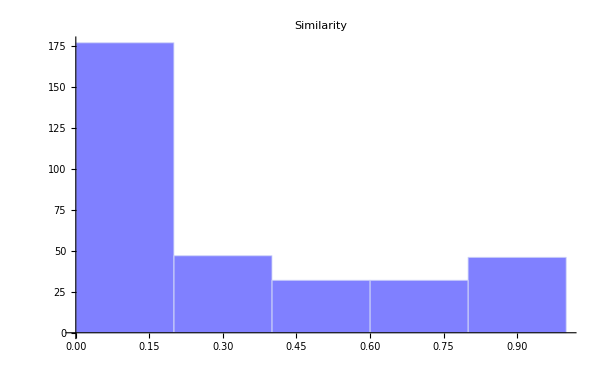

```mathematica
TimeHist = Histogram[TimeDat,{100},
PlotLabel->Style["Time to Sweep",25],
LabelStyle->Directive[Thick],
ImageSize->600,
ChartStyle->RGBColor[.5,.5,1],
AxesStyle->Directive[Thick,20]]
ClumpinessHist = Histogram[Clumpiness,
PlotLabel->Style["Clumpiness",25],
LabelStyle->Directive[Thick],
ImageSize->600,
ChartStyle->RGBColor[.5,.5,1],
AxesStyle->Directive[Thick,20]]
SimilarityHist = Histogram[SimilarityDat,{.2},
PlotLabel->Style["Similarity",25],
LabelStyle->Directive[Thick],
ImageSize->600,
ChartStyle->RGBColor[.5,.5,1],
AxesStyle->Directive[Thick,20]]
```